```mathematica
direct={344750000,344750000,1219750000,1219750000,2607860,1886839,3480544,1604565,1249993,4825721,358759,358812,1229196,1232504}
instruments={125767969,125500741,1374088126,1368728031,3549345.667,1836090.333,3608634.667,627143.3333,1101583,2980723,42628.33333,57033.33333,108023.6667,141827.6667}
```

{344750000,344750000,1219750000,1219750000,2607860,1886839,3480544,1604565,1249993,4825721,358759,358812,1229196,1232504}

{125767969,125500741,1374088126,1368728031,3.54935×10^6,1.83609×10^6,3.60863×10^6,627143.,1101583,2980723,42628.3,57033.3,108024.,141828.}

```mathematica
data=Transpose@{direct,instruments}
```

{{344750000,125767969},{344750000,125500741},{1219750000,1374088126},{1219750000,1368728031},{2607860,3.54935×10^6},{1886839,1.83609×10^6},{3480544,3.60863×10^6},{1604565,627143.},{1249993,1101583},{4825721,2980723},{358759,42628.3},{358812,57033.3},{1229196,108024.},{1232504,141828.}}

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[-3.24389×10^7+1.09989 x]

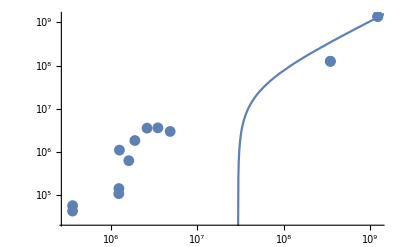

```mathematica
Show[ListLogLogPlot[data], LogLogPlot[model["BestFit"],{x,1,10^12}]]
```

```mathematica
model["RSquared"]
```

0.963248